5

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

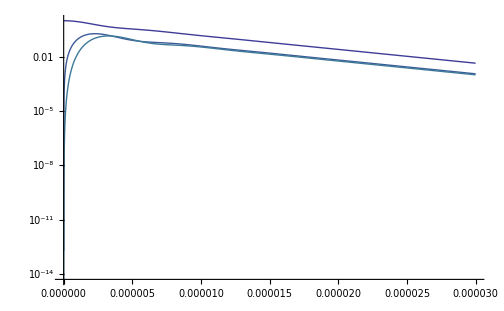

4.22049

```mathematica
n = 5
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
Γ1 = α η^2 n Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;
(*If[n == 1, Γ = Γ1+Γ2, dummy = 0]*)

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2=ρ22/.First[sol];
expsol = Solve[Re[fun3[6 10^-5  ]] == Re[fun3[1 10^-5 ]] Exp[-l 5 10^-5 ],l];
la = l /. expsol;
LogPlot[Evaluate[ρe[t]/.sol],{t,0,3*10*10^-6} , PlotRange -> All, PlotRange -> {Automatic, {10^-7,1}}]
```

```mathematica
Master equation for Raman- 3 level system
```

{equation for Master Raman-3 level (ρ11'[t]==(0.-9.48252×10^33 ⅈ) (0.-3.70409×10^-29 ρ12[t]+3.70409×10^-29 ρ21[t])+220800. ρ33[t]),equation for Master Raman-3 level (ρ12'[t]==(0.-9.48252×10^33 ⅈ) (0.-3.70409×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-1.02293×10^-28 ρ13[t]+3.70409×10^-29 ρ22[t])),equation for Master Raman-3 level (ρ13'[t]==-920000. ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-1.02293×10^-28 ρ12[t]+3.70409×10^-29 ρ23[t])),equation for Master Raman-3 level (ρ21'[t]==(0.-9.48252×10^33 ⅈ) (0.+3.70409×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-3.70409×10^-29 ρ22[t]+1.02293×10^-28 ρ31[t])),equation for Master Raman-3 level (ρ22'[t]==(0.-9.48252×10^33 ⅈ) (0.+3.70409×10^-29 ρ12[t]-3.70409×10^-29 ρ21[t]-1.02293×10^-28 ρ23[t]+1.02293×10^-28 ρ32[t])+471040. ρ33[t]),equation for Master Raman-3 level (ρ23'[t]==-920000. ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+3.70409×10^-29 ρ13[t]-1.02293×10^-28 ρ22[t]+1.05457×10^-34 ρ23[t]+1.02293×10^-28 ρ33[t])),equation for Master Raman-3 level (ρ31'[t]==-920000. ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+1.02293×10^-28 ρ21[t]-3.70409×10^-29 ρ32[t])),equation for Master Raman-3 level (ρ32'[t]==-920000. ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+1.02293×10^-28 ρ22[t]-3.70409×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-1.02293×10^-28 ρ33[t])),equation for Master Raman-3 level (ρ33'[t]==(0.-9.48252×10^33 ⅈ) (0.+1.02293×10^-28 ρ23[t]-1.02293×10^-28 ρ32[t])-1.84×10^6 ρ33[t])}

```mathematica
α = 0.6; ωR = 3 10^8*(2 Pi)/(455 10^-9);Γ = 1.84 10^6; Ωn = 2 Pi 30.6 10^3;δ1 = 1; δ2 = 1; δ12 = 0; η = 0.2;n = 1;hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ; Int = 180 10^-3/(10^-4); h = 2 Pi *hbar; c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
```

```mathematica
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}})
```

{{-1.05457×10^-34,1.01379×10^-29,0.},{1.01379×10^-29,0.,1.44664×10^-27},{0.,1.44664×10^-27,-1.05457×10^-34}}

```mathematica
Γ1 = α η^2 n Γ
Γ2 = (1-α)(1-η^2(2n - 1))Γ
```

44160.

706560.

```mathematica
Γ
```

1.84×10^6

```mathematica
Γo = Γ - Γ1 - Γ2;
```

```mathematica
L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}})
```

{{44160. ρ33[t],0,-920000. ρ13[t]},{0,706560. ρ33[t],-920000. ρ23[t]},{-920000. ρ31[t],-920000. ρ32[t],-1.84×10^6 ρ33[t]}}

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L)//FullSimplify
```

{{(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t])+44160. ρ33[t],(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-1.44664×10^-27 ρ13[t]+1.01379×10^-29 ρ22[t]),-920000. ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-1.44664×10^-27 ρ12[t]+1.01379×10^-29 ρ23[t])},{(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+1.44664×10^-27 ρ31[t]),(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-1.44664×10^-27 ρ23[t]+1.44664×10^-27 ρ32[t])+706560. ρ33[t],-920000. ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ13[t]-1.44664×10^-27 ρ22[t]+1.05457×10^-34 ρ23[t]+1.44664×10^-27 ρ33[t])},{-920000. ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ21[t]-1.01379×10^-29 ρ32[t]),-920000. ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-1.44664×10^-27 ρ33[t]),(0.-9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ23[t]-1.44664×10^-27 ρ32[t])-1.84×10^6 ρ33[t]}}

```mathematica
Clear[ρe]
```

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})]
```

{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}

```mathematica
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
```

```mathematica
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
```

```mathematica
numerical solution
```

numerical solution

```mathematica
ρe[t_] := {ρ11[t],ρ12[t],ρ13[t],ρ21[t],ρ22[t],ρ23[t],ρ31[t],ρ32[t],ρ33[t]};
init={ρ11[0] == 0, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 1};
Join[system,init]//N
```

{ρ11'[t]==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t])+44160. ρ33[t],ρ12'[t]==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-1.44664×10^-27 ρ13[t]+1.01379×10^-29 ρ22[t]),ρ13'[t]==-920000. ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-1.44664×10^-27 ρ12[t]+1.01379×10^-29 ρ23[t]),ρ21'[t]==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+1.44664×10^-27 ρ31[t]),ρ22'[t]==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-1.44664×10^-27 ρ23[t]+1.44664×10^-27 ρ32[t])+706560. ρ33[t],ρ23'[t]==-920000. ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ13[t]-1.44664×10^-27 ρ22[t]+1.05457×10^-34 ρ23[t]+1.44664×10^-27 ρ33[t]),ρ31'[t]==-920000. ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ21[t]-1.01379×10^-29 ρ32[t]),ρ32'[t]==-920000. ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-1.44664×10^-27 ρ33[t]),ρ33'[t]==(0.-9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ23[t]-1.44664×10^-27 ρ32[t])-1.84×10^6 ρ33[t],ρ11[0.]==0.,ρ12[0.]==0.,ρ13[0.]==0.,ρ21[0.]==0.,ρ22[0.]==0.,ρ23[0.]==0.,ρ31[0.]==0.,ρ32[0.]==0.,ρ33[0.]==1.}

```mathematica
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 10000]
```

{{ρ11→InterpolatingFunction[{{0.,1.}},<>],ρ12→InterpolatingFunction[{{0.,1.}},<>],ρ13→InterpolatingFunction[{{0.,1.}},<>],ρ21→InterpolatingFunction[{{0.,1.}},<>],ρ22→InterpolatingFunction[{{0.,1.}},<>],ρ23→InterpolatingFunction[{{0.,1.}},<>],ρ31→InterpolatingFunction[{{0.,1.}},<>],ρ32→InterpolatingFunction[{{0.,1.}},<>],ρ33→InterpolatingFunction[{{0.,1.}},<>]}}

```mathematica
LogPlot[Evaluate[ρe[t]/.sol],{t,0,10*10^-6} , PlotRange -> All, PlotLegends -> Automatic, PlotRange -> {Automatic, {-2,2}}]
```

LogPlot::optx: Unknown option PlotLegends → Automatic in LogPlot[{{« 1 »}}, {t, 0, 10/10^6}, PlotRange → All, PlotLegends → Automatic, PlotRange → {Automatic, {-2, 2}}].

LogPlot[{{InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t],InterpolatingFunction[{{0.,1.}},<>][t]}},{t,0,10/10^6},PlotRange→All,PlotLegends→Automatic,PlotRange→{Automatic,{-2,2}}]

```mathematica
fun=ρ33/.First[sol]
```

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
fun[0.0601]
```

1.6837×10^-8-1.00803×10^-28 ⅈ

```mathematica
Re[fun[0.061]]
```

1.55713×10^-8

```mathematica
Solve[Re[fun[8 10^-6]] == Re[fun[2 10^-6]] Exp[-l *6 10^-6],l]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→560718.}}

```mathematica
steady state solution
```

solution state steady

```mathematica
sol=DSolve[system,ρef2,t]
```

{{«1»}}

```mathematica
system = Table[0 == Part[dρdtf,j],{j,1,9,1}]
```

{0==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t])+44160. ρ33[t],0==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-1.44664×10^-27 ρ13[t]+1.01379×10^-29 ρ22[t]),0==-920000. ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-1.44664×10^-27 ρ12[t]+1.01379×10^-29 ρ23[t]),0==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+1.44664×10^-27 ρ31[t]),0==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-1.44664×10^-27 ρ23[t]+1.44664×10^-27 ρ32[t])+706560. ρ33[t],0==-920000. ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ13[t]-1.44664×10^-27 ρ22[t]+1.05457×10^-34 ρ23[t]+1.44664×10^-27 ρ33[t]),0==-920000. ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ21[t]-1.01379×10^-29 ρ32[t]),0==-920000. ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-1.44664×10^-27 ρ33[t]),0==(0.-9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ23[t]-1.44664×10^-27 ρ32[t])-1.84×10^6 ρ33[t]}

```mathematica
system
```

{0==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t])+44160. ρ33[t],0==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-1.44664×10^-27 ρ13[t]+1.01379×10^-29 ρ22[t]),0==-920000. ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-1.44664×10^-27 ρ12[t]+1.01379×10^-29 ρ23[t]),0==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+1.44664×10^-27 ρ31[t]),0==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-1.44664×10^-27 ρ23[t]+1.44664×10^-27 ρ32[t])+706560. ρ33[t],0==-920000. ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ13[t]-1.44664×10^-27 ρ22[t]+1.05457×10^-34 ρ23[t]+1.44664×10^-27 ρ33[t]),0==-920000. ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ21[t]-1.01379×10^-29 ρ32[t]),0==-920000. ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-1.44664×10^-27 ρ33[t]),0==(0.-9.48252×10^33 ⅈ) (0.+1.44664×10^-27 ρ23[t]-1.44664×10^-27 ρ32[t])-1.84×10^6 ρ33[t]}

```mathematica
Solve[system, ρef2]
```

{{ρ11[t]→0,ρ12[t]→0,ρ13[t]→0,ρ21[t]→0,ρ22[t]→0,ρ23[t]→0,ρ31[t]→0,ρ32[t]→0,ρ33[t]→0}}

```mathematica
no steady state solution as system is not closed, one can look at solutions with constant decay rates instead
```

```mathematica
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ωR}, {0, ωR, -2 δ2}})
```

{{-1.05457×10^-34,1.01379×10^-29,0.},{1.01379×10^-29,0.,2.18442×10^-19},{0.,2.18442×10^-19,-1.05457×10^-34}}

```mathematica
Γ1 = αeff  Γ;
Γ2 =  (1-αeff) Γ; Clear[Γ, ωR, n, η, hbar, Ωn, δ1, δ2, δ12]
```

```mathematica
L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}})
```

{{1.84×10^6 αeff ρ33[t],0,-1/2 Γ ρ13[t]},{0,1.84×10^6 (1-αeff) ρ33[t],-1/2 Γ ρ23[t]},{-1/2 Γ ρ31[t],-1/2 Γ ρ32[t],-Γ ρ33[t]}}

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
(*dρdt = -1/hbar(H. ρe[t]- ρe[t]. H)+ L //FullSimplify*)
dρdt = -ⅈ/hbar(H. ρe[t]- ρe[t]. H) //FullSimplify
```

{{-(ⅈ (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t]))/hbar,-(ⅈ (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-2.18442×10^-19 ρ13[t]+1.01379×10^-29 ρ22[t]))/hbar,-(ⅈ (0.-2.18442×10^-19 ρ12[t]+1.01379×10^-29 ρ23[t]))/hbar},{-(ⅈ (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+2.18442×10^-19 ρ31[t]))/hbar,-(ⅈ (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-2.18442×10^-19 ρ23[t]+2.18442×10^-19 ρ32[t]))/hbar,-(ⅈ (0.+1.01379×10^-29 ρ13[t]-2.18442×10^-19 ρ22[t]+1.05457×10^-34 ρ23[t]+2.18442×10^-19 ρ33[t]))/hbar},{-(ⅈ (0.+2.18442×10^-19 ρ21[t]-1.01379×10^-29 ρ32[t]))/hbar,-(ⅈ (0.+2.18442×10^-19 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-2.18442×10^-19 ρ33[t]))/hbar,-(ⅈ (0.+2.18442×10^-19 ρ23[t]-2.18442×10^-19 ρ32[t]))/hbar}}

```mathematica
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Table[0 == Part[dρdtf,j],{j,1,9,1}]//FullSimplify
```

{(ⅈ (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t]))/hbar==0,(ⅈ (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-2.18442×10^-19 ρ13[t]+1.01379×10^-29 ρ22[t]))/hbar==0,(ⅈ (0.-2.18442×10^-19 ρ12[t]+1.01379×10^-29 ρ23[t]))/hbar==0,(ⅈ (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+2.18442×10^-19 ρ31[t]))/hbar==0,(ⅈ (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-2.18442×10^-19 ρ23[t]+2.18442×10^-19 ρ32[t]))/hbar==0,(ⅈ (0.+1.01379×10^-29 ρ13[t]-2.18442×10^-19 ρ22[t]+1.05457×10^-34 ρ23[t]+2.18442×10^-19 ρ33[t]))/hbar==0,(ⅈ (0.+2.18442×10^-19 ρ21[t]-1.01379×10^-29 ρ32[t]))/hbar==0,(ⅈ (0.+2.18442×10^-19 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-2.18442×10^-19 ρ33[t]))/hbar==0,(ⅈ (0.+2.18442×10^-19 ρ23[t]-2.18442×10^-19 ρ32[t]))/hbar==0}

```mathematica
Solve[system, ρef2]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ρ13[t]→(-4.641×10^-11+0. ⅈ) ρ11[t]-(4.8277×10^-16+0. ⅈ) ρ12[t]+(4.641×10^-11+0. ⅈ) ρ22[t],ρ21[t]→(1.+0. ⅈ) ρ12[t],ρ23[t]→(2.15471×10^10+0. ⅈ) ρ12[t],ρ31[t]→(-4.641×10^-11+0. ⅈ) ρ11[t]-(4.8277×10^-16+0. ⅈ) ρ12[t]+(4.641×10^-11+0. ⅈ) ρ22[t],ρ32[t]→(2.15471×10^10+0. ⅈ) ρ12[t],ρ33[t]→(2.15389×10^-21+0. ⅈ) ρ11[t]-(0.0000104023+0. ⅈ) ρ12[t]+(1.+0. ⅈ) ρ22[t]}}

```mathematica
null := ({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})
```

```mathematica
Solve[null == dρdt, ρe]//FullSimplify
```

{}